# Kim Test Function

## GR Research Group

## Analytic Function

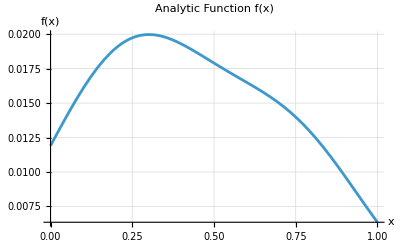

```mathematica
f[x_]:=f∞ (Sin[k1/L x]+Cos[k2/L x]);
f[x_]:=f∞ (1/k1 Exp[-Sqrt[k1]/L^2 (x-L/4)^2]+1/k2 Exp[-Sqrt[k2]/L^2 (x-(3 L)/4)^2])
f∞=1;
L=1;
k1=17 π;
k2=29 π;
Plot[f[x],{x,0,L},GridLines->Automatic,PlotLabel->"Analytic Function f(x)",AxesLabel->{"x","f(x)"}]
```

## Numerical Filter Operator

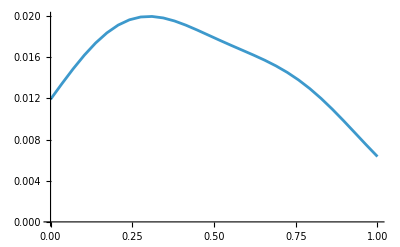

```mathematica
n=30; (*# of grid points*)
κc=0.9;
ϵ=0.05;

xList=Subdivide[0,L,n-1];
fN=Table[f[x],{x,xList}];
ListPlot[Transpose@{xList,fN},Joined->True]
```

```mathematica
kimPent6thFilters[n_,κc_,ϵ_,Matrix_]:=Module[{R,S, α, β,γ, bS,γS,b,a,A,c,d},
A=30-5Cos[κ]+10Cos[2κ]-3Cos[3κ];
α=-(30Cos[κ]+2Cos[3κ])/A;
β=(18+9Cos[κ]+6Cos[2κ]-Cos[3κ])/(2A);

a={0,30/A Cos[κ/2]^4,0,0};
a[[3]]=-(2a[[2]])/5;
a[[4]]=a[[2]]/15;
a[[1]]=-2(a[[2]]+a[[3]]+a[[4]]);

c=1+β(5+4β+60 β^2)+5(1+3β+10 β^2)α+2(4+11β)α^2+5 α^3;
d=(1-β)(1+6β+60 β^2)+(5+35β-29 β^2)α+(9-5β)α^2;

γ={{1,1/c(α(1+α)(1+4α)+2α(7+3α)β+24(1-α)β^2-80 β^3),1/c(α^3+(1+3α+14 α^2)β+46α β^2+60 β^3)},{1/d(10 β^2(8β-1)+(1+4β+81 β^2)α+5(1+8β)α^2+9 α^3),1,1/d(α(1+5α+9 α^2)+α(5+36α)β+(55α-1)β^2+10 β^3),β/d(1+5α+9 α^2+5(1+7α)β+50 β^2)},{β,α,1,α,β}};
γ[[1]]=γ[[1]]/.κ->(1-3ϵ)κc;
γ[[2]]=γ[[2]]/.κ->(1-2ϵ)κc;
γ[[3]]=γ[[3]]/.κ->(1-1ϵ)κc;

b={a[[3]]+5a[[4]],a[[2]]-10a[[4]],0,a[[2]]-5a[[4]],a[[3]]+a[[4]],a[[4]]}/.κ->(1-1ϵ)κc;
b[[3]]=-(Sum[b[[i]],{i,1,6}]);

β=β/.κ->κc;
α=α/.κ->κc;
a=a/.κ->κc;

R=IdentityMatrix[n];
R[[1,2]]=γ[[1,2]];R[[1,3]]=γ[[1,3]];
R[[2,1]]=γ[[2,1]]; R[[2,3]]=γ[[2,3]]; R[[2,4]]=γ[[2,4]];
R[[n,n-1]]=γ[[1,2]];R[[n,n-2]]=γ[[1,3]];
R[[n-1,n]]=γ[[2,1]]; R[[n-1,n-2]]=γ[[2,3]]; R[[n-1,n-3]]=γ[[2,4]];
R[[n-2,n]]=γ[[3,1]]; R[[n-2,n-1]]=γ[[3,2]]; R[[n-2,n-3]]=γ[[3,4]]; R[[n-2,n-4]]=γ[[3,5]];
Do[
If[(j==i-2)||(j==i+2), 
R[[i,j]]=β,
If[(j==i-1)||(j==i+1),
R[[i,j]]=α
]
],{i,3,n-3},{j,1,n}];

S=Table[0,{i,n},{j,n}];
Do[S[[3,i]]=b[[i]]; S[[n-2,n-i+1]]=b[[i]],{i,1,6}];
Do[
If[j>=i-3&&j<=i+3,
S[[i,j]]=a[[Abs[i-j]+1]]
]
,{i,4,n-3},{j,1,n}];

If[Matrix,
Return[{R,S}],
Return[{"α"->α, "β"->β, "a0"->a[[1]],"a1"->a[[2]],"a2"->a[[3]],"a3"->a[[4]],"γ01"->γ[[1,2]],"γ02"->γ[[1,3]], "γ10"->γ[[2,1]],"γ12"->γ[[2,3]],"γ13"->γ[[2,4]],"γ20"->γ[[3,1]],"γ21"->γ[[3,2]],"γ23"->γ[[3,4]],"γ24"->γ[[3,5]],"b20"->b[[1]],"b21"->b[[2]],"b22"->b[[3]],"b23"->b[[4]],"b24"->b[[5]],"b25"->b[[6]]}]
]
]
```

```mathematica
{R,S}=kimPent6thFilters[n,κc,ϵ,True];
(*I think we need to not be striking a row and column*)
R//MatrixForm;
S//MatrixForm;
(*R Δ̂ f = S f*)
(* Δ̂ f = R^-1 S f*)
ΔHatf=Inverse[R].S.fN;
```

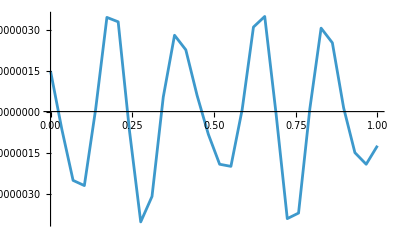

```mathematica
ListPlot[Transpose@{xList,ΔHatf},Joined->True]
```

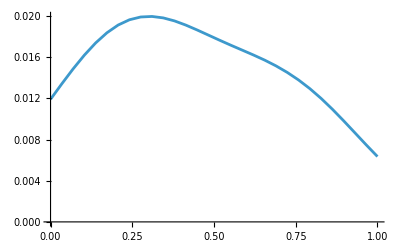

```mathematica
fHat=fN+ΔHatf;
ListPlot[Transpose@{xList,fHat},Joined->True]
```

## Error Analysis

```mathematica
Error=Sqrt[Sum[(ΔHatf[[i]])^2,{i,1,n}]/((f∞)^2 (n+1))]
```

3.38359×10^-8

## Loop

```mathematica
kimPent6thFilters[n_,κc_,ϵ_,Matrix_]:=Module[{R,S, α, β,γ, bS,γS,b,a,A,c,d},
A=30-5Cos[κ]+10Cos[2κ]-3Cos[3κ];
α=-(30Cos[κ]+2Cos[3κ])/A;
β=(18+9Cos[κ]+6Cos[2κ]-Cos[3κ])/(2A);

a={0,30/A Cos[κ/2]^4,0,0};
a[[3]]=-(2a[[2]])/5;
a[[4]]=a[[2]]/15;
a[[1]]=-2(a[[2]]+a[[3]]+a[[4]]);

c=1+β(5+4β+60 β^2)+5(1+3β+10 β^2)α+2(4+11β)α^2+5 α^3;
d=(1-β)(1+6β+60 β^2)+(5+35β-29 β^2)α+(9-5β)α^2;

γ={{1,1/c(α(1+α)(1+4α)+2α(7+3α)β+24(1-α)β^2-80 β^3),1/c(α^3+(1+3α+14 α^2)β+46α β^2+60 β^3)},{1/d(10 β^2(8β-1)+(1+4β+81 β^2)α+5(1+8β)α^2+9 α^3),1,1/d(α(1+5α+9 α^2)+α(5+36α)β+(55α-1)β^2+10 β^3),β/d(1+5α+9 α^2+5(1+7α)β+50 β^2)},{β,α,1,α,β}};
γ[[1]]=γ[[1]]/.κ->(1-3ϵ)κc;
γ[[2]]=γ[[2]]/.κ->(1-2ϵ)κc;
γ[[3]]=γ[[3]]/.κ->(1-1ϵ)κc;

b={a[[3]]+5a[[4]],a[[2]]-10a[[4]],0,a[[2]]-5a[[4]],a[[3]]+a[[4]],a[[4]]}/.κ->(1-1ϵ)κc;
b[[3]]=-(Sum[b[[i]],{i,1,6}]);

β=β/.κ->κc;
α=α/.κ->κc;
a=a/.κ->κc;

R=IdentityMatrix[n];
R[[1,2]]=γ[[1,2]];R[[1,3]]=γ[[1,3]];
R[[2,1]]=γ[[2,1]]; R[[2,3]]=γ[[2,3]]; R[[2,4]]=γ[[2,4]];
R[[n,n-1]]=γ[[1,2]];R[[n,n-2]]=γ[[1,3]];
R[[n-1,n]]=γ[[2,1]]; R[[n-1,n-2]]=γ[[2,3]]; R[[n-1,n-3]]=γ[[2,4]];
R[[n-2,n]]=γ[[3,1]]; R[[n-2,n-1]]=γ[[3,2]]; R[[n-2,n-3]]=γ[[3,4]]; R[[n-2,n-4]]=γ[[3,5]];
Do[
If[(j==i-2)||(j==i+2), 
R[[i,j]]=β,
If[(j==i-1)||(j==i+1),
R[[i,j]]=α
]
],{i,3,n-3},{j,1,n}];

S=Table[0,{i,n},{j,n}];
Do[S[[3,i]]=b[[i]]; S[[n-2,n-i+1]]=b[[i]],{i,1,6}];
Do[
If[j>=i-3&&j<=i+3,
S[[i,j]]=a[[Abs[i-j]+1]]
]
,{i,4,n-3},{j,1,n}];

If[Matrix,
Return[{R,S}],
Return[{"α"->α, "β"->β, "a0"->a[[1]],"a1"->a[[2]],"a2"->a[[3]],"a3"->a[[4]],"γ01"->γ[[1,2]],"γ02"->γ[[1,3]], "γ10"->γ[[2,1]],"γ12"->γ[[2,3]],"γ13"->γ[[2,4]],"γ20"->γ[[3,1]],"γ21"->γ[[3,2]],"γ23"->γ[[3,4]],"γ24"->γ[[3,5]],"b20"->b[[1]],"b21"->b[[2]],"b22"->b[[3]],"b23"->b[[4]],"b24"->b[[5]],"b25"->b[[6]]}]
]
];
```

```mathematica
κcList={0.5,0.7,0.9};
ϵList={0,0.05,0.10};
nList={30,100,300};
```

```mathematica
results=Table[κc=κcList[[j]];
Table[
n=nList[[i]];
ϵ=ϵList[[k]];

xList=Subdivide[0,L,n-1];
fN=Table[f[x],{x,xList}];

{R,S}=kimPent6thFilters[n,κc,ϵ,True];
ΔHatf=Inverse[R].S.fN;
Error=Sqrt[Sum[(ΔHatf[[i]])^2,{i,1,n}]/((f∞)^2 (n+1))];
{{κc,ϵ},{n,Error}},
{k,1,Length@ϵList},{i,1,Length@nList}],
{j,1,Length@κcList}]
```

{{{{{0.5,0},{30,0.0000987596}},{{0.5,0},{100,1.05725×10^-7}},{{0.5,0},{300,4.85652×10^-10}}},{{{0.5,0.05},{30,7.80477×10^-6}},{{0.5,0.05},{100,1.27754×10^-8}},{{0.5,0.05},{300,5.15015×10^-11}}},{{{0.5,0.1},{30,4.06892×10^-6}},{{0.5,0.1},{100,6.59711×10^-9}},{{0.5,0.1},{300,2.70266×10^-11}}}},{{{{0.7,0},{30,0.0000148835}},{{0.7,0},{100,4.12617×10^-9}},{{0.7,0},{300,4.76828×10^-11}}},{{{0.7,0.05},{30,3.89927×10^-6}},{{0.7,0.05},{100,2.62341×10^-8}},{{0.7,0.05},{300,3.6159×10^-10}}},{{{0.7,0.1},{30,2.36727×10^-6}},{{0.7,0.1},{100,8.38083×10^-7}},{{0.7,0.1},{300,1.69705×10^-11}}}},{{{{0.9,0},{30,4.94259×10^-7}},{{0.9,0},{100,5.46682×10^-9}},{{0.9,0},{300,1.91461×10^-11}}},{{{0.9,0.05},{30,2.27998×10^-6}},{{0.9,0.05},{100,3.60265×10^-9}},{{0.9,0.05},{300,5.49636×10^-11}}},{{{0.9,0.1},{30,7.65074×10^-7}},{{0.9,0.1},{100,1.35288×10^-9}},{{0.9,0.1},{300,2.56937×10^-11}}}}}

## Convergence Plot

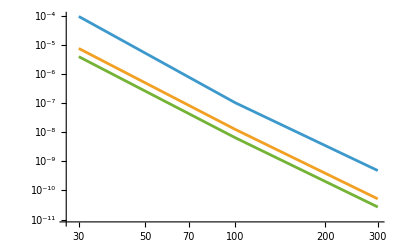

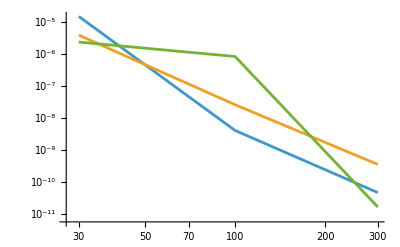

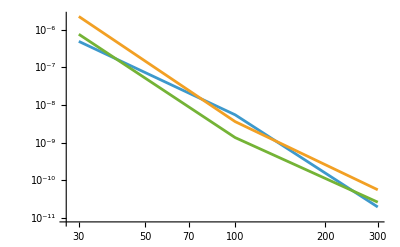

```mathematica
green=Table[(Transpose@results[[1,x]])[[2]],{x,1,3}];
red=Table[(Transpose@results[[2,x]])[[2]],{x,1,3}];
blue=Table[(Transpose@results[[3,x]])[[2]],{x,1,3}];
ListLogLogPlot[green,Joined->True]
ListLogLogPlot[red,Joined->True]
ListLogLogPlot[blue,Joined->True]
```

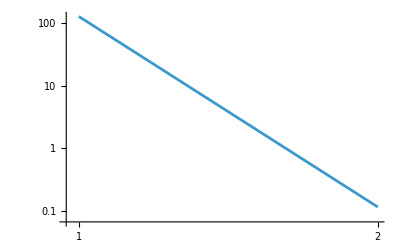

```mathematica
κcList={0.5,0.7,0.9};
ϵList={0,0.05,0.10};
nList={30,100,300,1000,3000};

(*This needs some modifying*)
ListLogLogPlot[Transpose@{n,Error},Joined->True]
```